Zadatak 1. Napisati program približno računa ∫_a^b f(x)ⅆx složenom Simpsonovom formulom.

```mathematica
sf[f_,x_,a_,b_,m_]:=Module[{h,s},
h=(b-a)/(2m)//N;
s=f/.x->a;
Do[
s=s+2(f/.x->a+2i*h)+4(f/.x->a+(2i-1)*h),
{i,1,m-1}];
s=s+4(f/.x->a+(2m-1)*h)+f/.x->b;
s=s*h/3
]
```

```mathematica
sf[E^(-x^2),x,0,1,5]
```

0.746825

```mathematica
NIntegrate[E^(-x^2),{x,0,1}]
```

0.746824

```mathematica
cetvrti[x_]=D[E^(-x^2),{x,4}]
```

12 ⅇ^(-x^2)-48 ⅇ^(-x^2) x^2+16 ⅇ^(-x^2) x^4

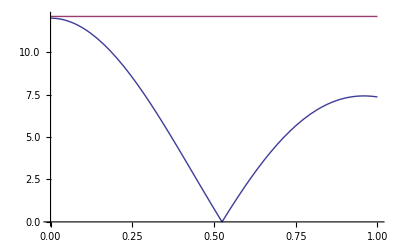

```mathematica
Plot[{Abs[cetvrti[x]],12.1},{x,0,1}]
```

```mathematica
M4=Abs[cetvrti[0]]
```

12

```mathematica
greska=1/180 M4*(1/10)^4//N
```

6.66667×10^-6

Zadatak 2. Metodom polovljenja približno rešiti jednačinu cos 5x-7x+1=0, sa tačnošću ne manjom od 10^-3.

```mathematica
f[x_]=Cos[5x]-7x+1
```

1-7 x+Cos[5 x]

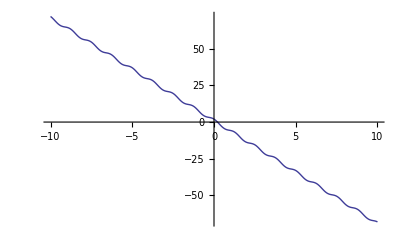

```mathematica
Plot[f[x],{x,-10,10}]
```

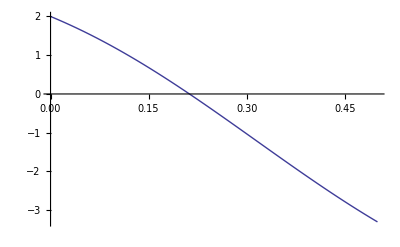

```mathematica
Plot[f[x],{x,0,0.5}]
```

```mathematica
f[0]*f[0.5]
```

-6.60229

```mathematica
a=0;b=0.5;
```

```mathematica
While[Abs[b-a]>10^-3&&f[(a+b)/2]≠ 0,
If[(f[a])*(f[(a+b)/2])<0,
b=(a+b)/2,
a=(a+b)/2
];
]
Print["[",a,",",b,"]"]
```

[0.211914,0.212891]

Zadatak 3. Opštim iterativnim postupkom rešiti jednačinu cos 5x-7x+1=0. Postupak se završava kada je apsolutna razlika dve uzastopne iteracije manja od 10^-4.

```mathematica
f[x_]=Cos[5x]-7x+1
```

1-7 x+Cos[5 x]

```mathematica
Plot[f[x],{x,0,0.5}]
```

-Graphics-

```mathematica
f[0]*f[0.5]<0
```

True

```mathematica
g[x_]=(Cos[5x]+1)/7
```

1/7 (1+Cos[5 x])

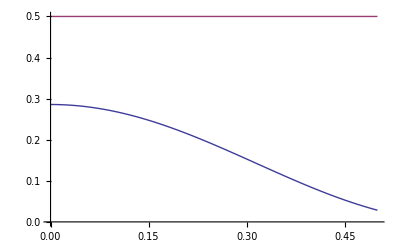

```mathematica
Plot[{g[x],0.5},{x,0,0.5}]
```

```mathematica
(*funkcija g:[0,0.5]->[0,0.5]*)
prvi[x_]=D[g[x],x]
```

-5/7 Sin[5 x]

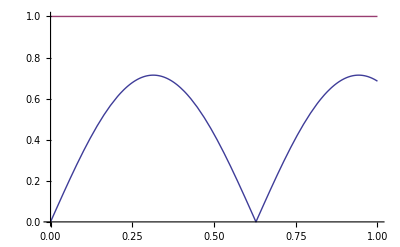

```mathematica
Plot[{Abs[prvi[x]],1},{x,0,1}]
```

```mathematica
(*|g(x)|<1, za xϵ[0,0.5]*)
iter[0]=0//N;
iter[1]=g[iter[0]];
i=1;
While[Abs[iter[i]-iter[i-1]]>10^-4,
iter[i+1]=g[iter[i]];
i=i+1;
];
Table[iter[k],{k,0,i}]
```

{0.,0.285714,0.163107,0.240783,0.194101,0.223555,0.205384,0.21678,0.209698,0.214126,0.211368,0.21309,0.212016,0.212686,0.212268,0.212529,0.212366,0.212468,0.212404}

```mathematica
NestList[g,0,10]//N
```

{0.,0.285714,0.163107,0.240783,0.194101,0.223555,0.205384,0.21678,0.209698,0.214126,0.211368}

Zadatak 4. Napisati program koji jednačinu f(x)=0, uz početnu iteraciju x_0 Njutnovim postupkom uz izlazni kriterijum |x_k-x_(k-1)|≤atol, gde je atol data vrednost.